Symbolic integration of the cosine-weighted constant visibility function ∫cosθ sinθⅆθ= -1/2 cos^2 θ
Integration over the entire hemisphere ∫_0^(2π) ∫_0^(π/2) cosθ sinθⅆθⅆϕ=π

```mathematica
2π * Integrate[Cos[θ]Sin[θ],{θ,0,π/2}]
```

π

We can then assume that the Ambient Occlusion value of a flat, unoccluded surface should equal π, which is then scaled to 1 to be stored into a classical AO texture.
So let’s decide that an AO map’s value should be scaled by π when read by a shader, multiplied by ρ/πthe surface’s albedo to obtain a [0,1] ambient reflectance value, then multiplied by the irradiance perceived by the surface to finally obtain the reflected radiance in the outgoing direction ω_o:
	L(x,ω_o) = ρ/π (π AO)E(x)=ρ AO E(x)

We can write the “direct” irradiance estimate as:
	E_0(x)=∫_Ω^□ L_0 V_dir(ω_i)(n.ω_i)ⅆ ω_i
Where L_0=1 and V_dir(ω_i) represents the direct visibility function that equals 1 if the ray is unoccluded by the surface, 0 otherwise.
We notice that E_0(x) is exactly the value computed for the Ambient Occlusion, so E_0(x)=AO.

We can then write the general expression for the “indirect” irradiance estimate as:
	E_(n+1)(x)=∫_Ω^□ L_i(x,ω_i )V_ind(ω_i)(n.ω_i)ⅆ ω_i
Where V_ind(ω_i) represents the indirect visibility function that equals 1 if the ray is occluded by the surface, 0 otherwise (so V_ind(ω_i)=1-V_dir(ω_i) ).
We can rewrite the perceived incoming luminance L_i(x,ω_i ) from a neighbor location x' as:
	L_i(x,ω_i )=ρ/π E_n(x')
And finally:
	E_(n+1)(x)=∫_Ω^□ ρ/π E_n(x')V_ind(ω_i)(n.ω_i)ⅆ ω_i

We easily see that we can compute the irradiance incrementally by re-using the previous irradiance at the indirect neighbor locations.

## Fitting Experimental Data

After writing the program that computes the AO and the multiple indirect bounces from a height map, we collect the bounced illuminance values into histograms where the bin indices are given by the AO values: this bascially computes the average indirect illuminance perceived by a point given its AO value (AO value is in [0,π] but we rescaled it to [0,1] for convenience).
We do that for multiple bounces to try and find a pattern in the shape and amplitude of the curves...

To generate the curves shown below, we used the WallHeight.png as a height map, and its corresponding WallNormal.png as a normal map.
We also chose a height value of 5 cm for a total wall length of 1 meter, 1024 rays at 179° cone aperture.
It gave some nice curves without the annoying artefacts found at the extremas that can be found with other maps.

```mathematica
ClearAll["Global`*"]
```

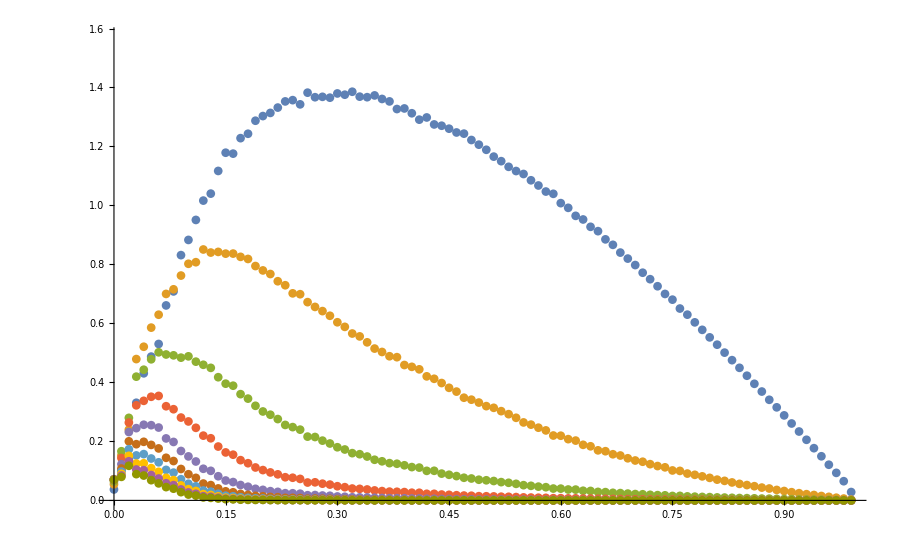

```mathematica
SetDirectory[NotebookDirectory[]]; 
tableSize = 100;
bouncesCount = 10;
rawArray=Table[ BinaryReadList["WallHeight"<>ToString[i]<>".float", "Real32"],{i,1,bouncesCount}];
bounces = Table[Table[{(i-1)/tableSize,rawArray[[bounceIndex]][[i]]},{i,1,tableSize}],{bounceIndex,1,bouncesCount}];
ListPlot[bounces,PlotRange->{0,π/2}]
```

Intuitively, it looks like a log-normal distribution curve that we can model as f(x)=a*x*(1-x)*e^-bx.
We can see below that it’s actually a very nice fit for the curves and may even deduce a general rule to find a and b coefficients as a function of the bounce index...

```mathematica
Manipulate[Plot[8*x*(1-x)*ⅇ^(-k*x),{x,0,1},PlotRange->{0,π/2}],{{k,1},0,20}]
```

```mathematica
Clear[a,b]
model=b/a*x*(1-x)*Exp[-b*x];
fitter[i_]:=Module[{},
FindFit[bounces[[i]], model,{a,{b,20}},{x}]
]
fits=Table[fitter[bounceIndex],{bounceIndex,1,bouncesCount}]
```

{{a→0.145266,b→1.55043},{a→0.360125,b→4.9367},{a→0.662865,b→9.62783},{a→1.00588,b→16.3854},{a→1.36116,b→22.712},{a→1.74407,b→27.4423},{a→2.15167,b→31.166},{a→2.57505,b→34.4689},{a→3.00497,b→37.6836},{a→3.43309,b→40.9832}}

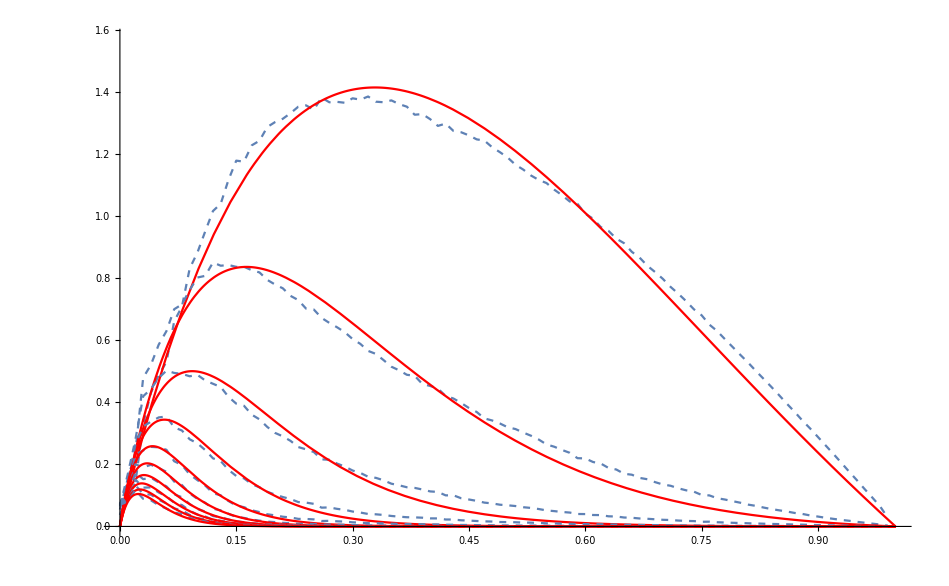

```mathematica
Show[
Table[{ListLinePlot[bounces[[bounceIndex]],PlotRange->{{0,1},{0,π/2}},PlotStyle->Dashed],
Plot[model/.fits[[bounceIndex]],{x,0,1},PlotRange->Full,PlotStyle->Red]},{bounceIndex,1,bouncesCount}]
]
```

Now we plot the various a and b coefficients as a function of the bounce index:

{0.145266,0.360125,0.662865,1.00588,1.36116,1.74407,2.15167,2.57505,3.00497,3.43309}

{1.55043,4.9367,9.62783,16.3854,22.712,27.4423,31.166,34.4689,37.6836,40.9832}

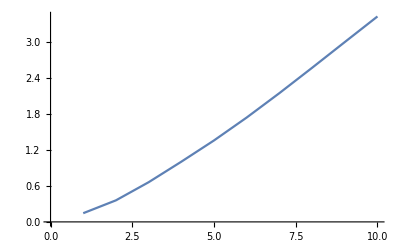

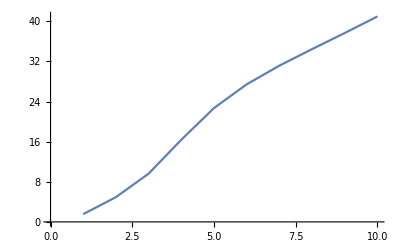

```mathematica
coeffsA=Table[a/.fits[[bounceIndex]],{bounceIndex,1,bouncesCount}]
coeffsB=Table[b/.fits[[bounceIndex]],{bounceIndex,1,bouncesCount}]
ListLinePlot[coeffsA,PlotRange->Full]
ListLinePlot[coeffsB,PlotRange->Full]
```

We notice the curves are almost linear so let’s try and fit the a and b coefficients as a linear function of the bounce index:

{a0→0.,a1→0.251994,a2→0.0130302}

FindFit::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{b0→1.,b1→1.,b2→1.,b3→1.}

Function[{x},1.55043+3.93698 (-1+x)]

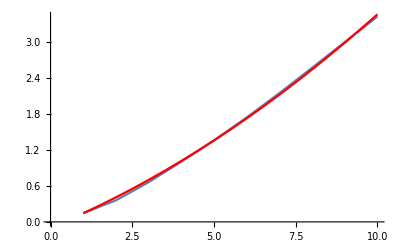

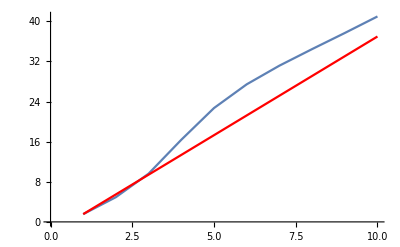

```mathematica
modelA=coeffsA[[1]]+0*a0+a1*(x-1)+a2*(x-1)^2;
modelB=coeffsB[[1]]+0*b0+b1*(x-1)+b2*(x-1)^2+b3*(x-1)^3;
modelB=coeffsB[[1]]+0*b0+b1*(x-1);
modelB=coeffsB[[1]]+(x-1)/(bouncesCount-1)*(coeffsB[[bouncesCount]] - coeffsB[[1]] - 4);
modelFitA=FindFit[coeffsA,modelA,{a0,a1,a2},{x}]
modelFitB=FindFit[coeffsB,modelB,{b0,b1,b2,b3},{x}]
(*Show[ListPlot[coeffsA,PlotRange->Full],Plot[modelA/.modelFitA,{x,0,bouncesCount}]]
Show[ListPlot[coeffsB,PlotRange->Full],Plot[modelB/.modelFitB,{x,0,bouncesCount}]]*)

modelFitA=Function[{x},Evaluate[modelA/.modelFitA]];
modelFitB=Function[{x},Evaluate[modelB/.modelFitB]]
Show[ListLinePlot[coeffsA,PlotRange->Full],Plot[modelFitA[x],{x,1,bouncesCount},PlotStyle->Red]]
Show[ListLinePlot[coeffsB,PlotRange->Full],Plot[modelFitB[x],{x,1,bouncesCount},PlotStyle->Red]]
```

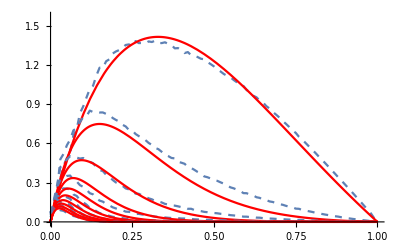

```mathematica
Show[
Table[{ListLinePlot[bounces[[bounceIndex]],PlotRange->{{0,1},{0,π/2}},PlotStyle->Dashed],
Plot[model/.{a-> modelFitA[bounceIndex],b-> modelFitB[bounceIndex]},{x,0,1},PlotRange->Full,PlotStyle->Red]},{bounceIndex,1,bouncesCount}]
]
```

{10.673,13.7083,14.5246,16.2896,16.6857,15.7346,14.4846,13.3858,12.5404,11.9377}

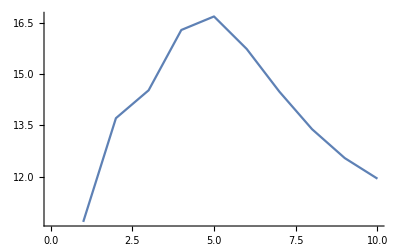

```mathematica
finalCoeffs=Table[coeffsB[[i]]/coeffsA[[i]],{i,1,bouncesCount}]
ListLinePlot[finalCoeffs]
```

## Refitting with Constrained b

Assuming b=?? we can try and re-fit the remaining variable a:

```mathematica
Clear[a,b]
fitter[i_]:=Module[{},
b = modelFitB[i];
FindFit[bounces[[i]], model,{a},{x}]
];
fits=Table[fitter[bounceIndex],{bounceIndex,1,bouncesCount}];
newCoeffsA=Table[a/.fits[[bounceIndex]],{bounceIndex,1,bouncesCount}]
Clear[a,b]
```

{0.145266,0.354521,0.667576,1.10147,1.56096,1.99283,2.40315,2.80657,3.20964,3.6127}

0.145266+0.385271 (-1+x)

0.145266+a0 (-1+x)+a1 (-1+x)^2

0.145266+a0 (-1+x)+a1 (-1+x)^2+a2 (-1+x)^3

{a0→0.19848,a1→0.048556,a2→-0.00312863}

a0→0.19848

a1→0.024278

{a0→0.19848,a1→0.024278,a2→0.}

Function[{x},0.145266+0.19848 (-1+x)+0.024278 (-1+x)^2]

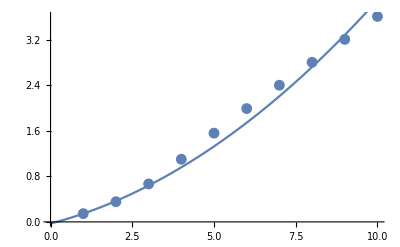

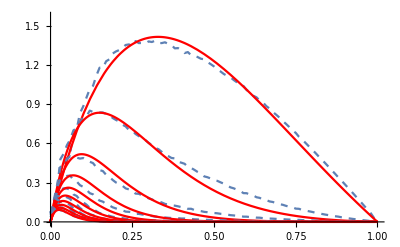

```mathematica
Clear[a0,a1,a2]
modelA=newCoeffsA[[1]]+(x-1)/(bouncesCount-1)*(newCoeffsA[[bouncesCount]]-newCoeffsA[[1]])
modelA=newCoeffsA[[1]]+a0*(x-1)+a1*(x-1)^2
modelA=newCoeffsA[[1]]+a0*(x-1)+a1*(x-1)^2+a2*(x-1)^3
modelFitA=FindFit[newCoeffsA,modelA,{a0,a1,a2},{x}]
modelFitA[[1]]=a0-> 1.0*(a0/.modelFitA[[1]])
modelFitA[[2]]=a1-> 0.5*(a1/.modelFitA[[2]])
modelFitA[[3]]=a2-> 0.0;
modelFitA
modelFitA=Function[{x},Evaluate[modelA/.modelFitA]]
Show[ListPlot[newCoeffsA,PlotRange->Full],Plot[modelFitA[x],{x,0,bouncesCount}]]
Clear[a,b]
Show[
Table[{ListLinePlot[bounces[[bounceIndex]],PlotRange->{{0,1},{0,π/2}},PlotStyle->Dashed],
Plot[model/.{ b-> modelFitB[bounceIndex],a->modelFitA[bounceIndex]},{x,0,1},PlotRange->Full,PlotStyle->Red]},{bounceIndex,1,bouncesCount}]
]
```

Reference graph without manual change of fitting variables (a0,a1,a2):

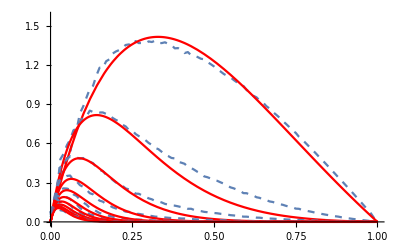

-Graphics-

## Using Fitted Data

Okay so we ended up with these expressions for a and b coefficients depending on i, the bounce index:
	a=0.145266+0.19848 (i-1)+0.024278 (i-1)^2
	b=1.55043+3.93698 (i-1)

We plug these into the reflectance model depending on α=AO/π:
	f(α,i)=b/a*α*(1-α)*ⅇ^(-b α)

As agreed, we assume the surface albedo ρ is constant in the surrounding of the luminance estimate and we can compute the final luminance due to indirect bounce on the surface as:

	L_indirect(x,ω_o) = 1/π[ρ AO(x) + ∑_(i=1)^N ρ^i f((AO(x))/π,i)]  E(x)

We notice the interesting property of albedo saturation as the amount of bounces increases.

## Verifying

We open the experimental ρ = 0.5 curves:

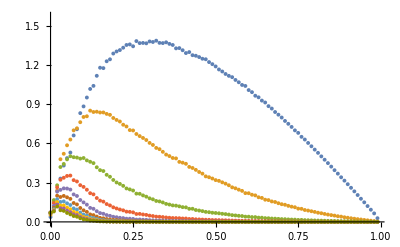

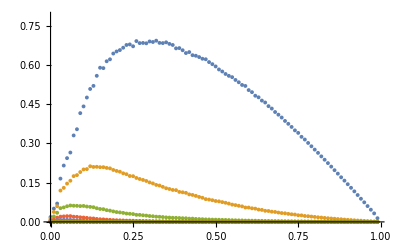

```mathematica
rawArray05=Table[ BinaryReadList["WallHeight"<>ToString[i]<>" - rho=0.5.float", "Real32"],{i,1,bouncesCount}];
bounces05 = Table[Table[{(i-1)/tableSize,rawArray05[[bounceIndex]][[i]]},{i,1,tableSize}],{bounceIndex,1,bouncesCount}];
ListPlot[bounces,PlotRange->{0,π/2}]
ListPlot[bounces05,PlotRange->{0,π/4}]
```

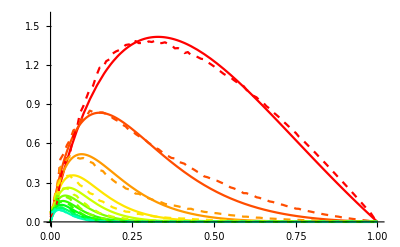

```mathematica
a[i_]:=0.14526642906187737+0.1984799936582921 (i-1)+0.024277999559107394 (i-1)^2
b[i_]:=1.5504282580946984+3.936979219376581 (i-1)
f[α_,i_]:=b[i]/a[i] α(1-α)ⅇ^(-b[i]α)
Show[Table[Plot[f[x,i],{x,0,1},PlotRange->{{0,1},{0,π/2}},PlotStyle->Hue[(i-1)/20]],{i,1,10}],
Table[ListLinePlot[bounces[[i]],PlotRange->Full,PlotStyle->{Dashed,Hue[(i-1)/20]}],{i,1,10}]]
```

And now for the moment of truth:

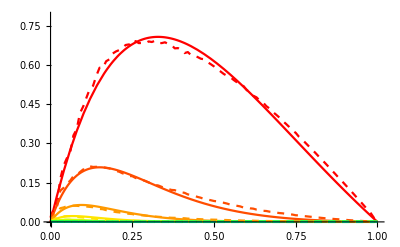

```mathematica
ρ=0.5;
Show[Table[Plot[ρ^i* f[x,i],{x,0,1},PlotRange->{{0,1},{0,π/4}},PlotStyle->Hue[(i-1)/20]],{i,1,10}],
Table[ListLinePlot[bounces05[[i]],PlotRange->Full,PlotStyle->{Dashed,Hue[(i-1)/20]}],{i,1,10}]]
```

## Let’s try and model a bounce function from its predecessor

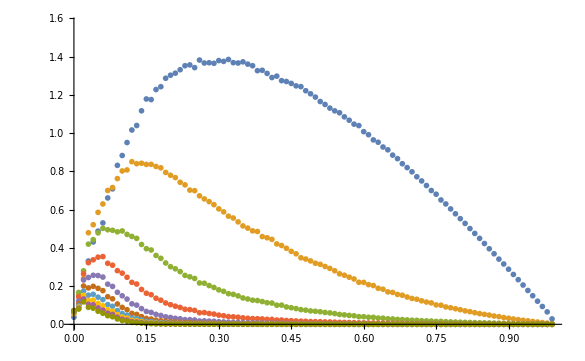

```mathematica
ListPlot[bounces,PlotRange->{0,π/2}]
```

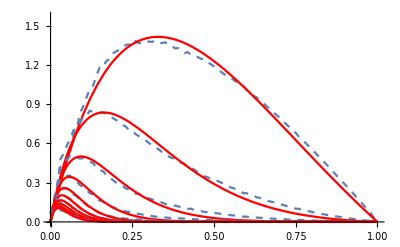

```mathematica
Clear[a,b]
model=b/a*x*(1-x)*Exp[-b*x];
fitter[i_]:=Module[{},
FindFit[bounces[[i]], model,{a,{b,20}},{x}]
]
fits=Table[fitter[bounceIndex],{bounceIndex,1,bouncesCount}];
Show[
Table[{ListLinePlot[bounces[[bounceIndex]],PlotRange->{{0,1},{0,π/2}},PlotStyle->Dashed],
Plot[model/.fits[[bounceIndex]],{x,0,1},PlotRange->Full,PlotStyle->Red]},{bounceIndex,1,bouncesCount}]
]
```

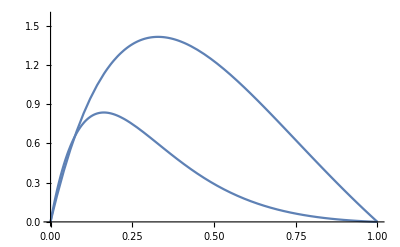

```mathematica
(* Build initial bounce function *)
f1=Function[{x},model/.fits[[1]]];
f2=Function[{x},model/.fits[[2]]];
Show[Plot[f1[x],{x,0,1},PlotRange->{0,π/2}],
Plot[f2[x],{x,0,1},PlotRange->{0,π/2}]]
(* Find how much f2 can be deduced from f1 by multiplying by an exponential *)
```

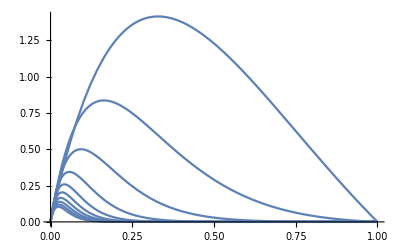

```mathematica
evals=Table[model/.fits[[bounceIndex]],{bounceIndex,1,bouncesCount}];
functor[i_]:=Module[{},
Function[{x},evals[[i]]]
]
funcs=Table[functor[bounceIndex],{bounceIndex,1,bouncesCount}];
Plot[funcs[[2]][x],{x,0,1}];
Show[Table[Plot[evals[[i]]/.x-> t,{t,0,1},PlotRange->All],{i,1,10}]];
Show[Table[Plot[funcs[[i]][x],{x,0,1},PlotRange->All],{i,1,10}]]
```

{a→1.28439,b→3.38627}

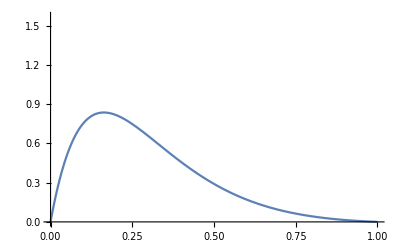

```mathematica
divModel=f1[x]*a*Exp[-b*x];
fit2=FindFit[bounces[[2]], divModel,{a,{b,20}},{x}]
fact2=Function[{x},divModel/.fit2];
Plot[fact2[x],{x,0,1},PlotRange->{0,π/2}]
```

{a→1.28439,b→3.38627}

{{a→1.28439,b→3.38627},{a→1.05955,b→4.69113},{a→1.12152,b→6.75756},{a→1.02432,b→6.32656},{a→0.942998,b→4.73031},{a→0.920554,b→3.72372},{a→0.924139,b→3.30294},{a→0.936848,b→3.21469},{a→0.951939,b→3.29962}}

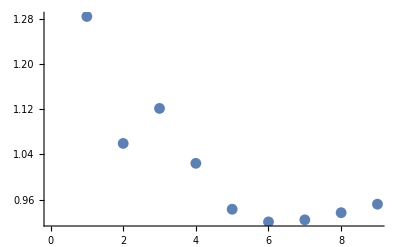

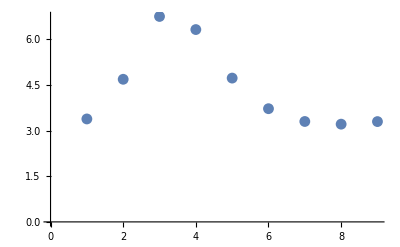

```mathematica
divModel=fprev*a*Exp[-b*x];
divFit=FindFit[bounces[[2]], divModel/.{fprev->f1[x]},{a,{b,1}},{x}]
divCoeffs=Table[FindFit[bounces[[bounceIndex]], divModel/.{fprev->funcs[[bounceIndex-1]][x]},{a,{b,20}},{x}],{bounceIndex,2,bouncesCount}]
ListPlot[a/.divCoeffs]
ListPlot[b/.divCoeffs]
```

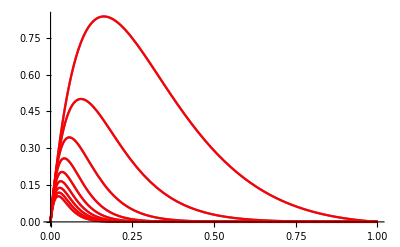

```mathematica
Show[
Table[Plot[funcs[[i]][x],{x,0,1},PlotRange->All],{i,2,bouncesCount}],
Table[Plot[funcs[[i-1]][x]*(a*Exp[-b*x]/.divCoeffs[[i-1]]),{x,0,1},PlotStyle->Red,PlotRange->All],{i,2,bouncesCount}]
]
```

Let’s fix b to a constant so we’re left with multiplying by a constant exponential value and coefficient a:

4.38

4.

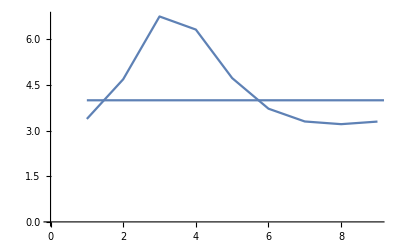

```mathematica
Clear[h]
defB = h/.FindFit[b/.divCoeffs,h,{h},{x}];
defB = 4.38
defB = 4.0
Show[ListLinePlot[b/.divCoeffs,PlotRange->All],Plot[defB,{x,1,bouncesCount},PlotRange->All]]
```

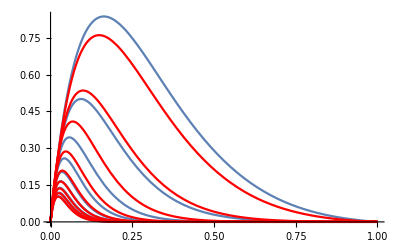

```mathematica
Show[
Table[Plot[funcs[[i]][x],{x,0,1},PlotRange->All],{i,2,bouncesCount}],
Table[Plot[funcs[[i-1]][x]*(a*Exp[-defB*x]/.divCoeffs[[i-1]]),{x,0,1},PlotStyle->Red,PlotRange->All],{i,2,bouncesCount}]
]
```

We see that now the amplitude coefficients a are a bit off so we need to recompute them with fixed factor b:

{{a→0.680573},{a→1.04274},{a→1.16286},{a→1.14321},{a→1.10282},{a→1.0725},{a→1.05111},{a→1.03584},{a→1.0248}}

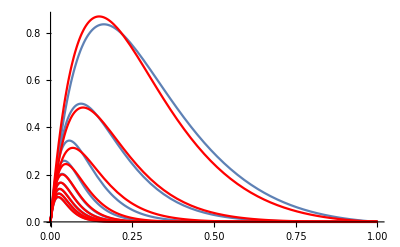

```mathematica
divModel=fprev*1/a*Exp[-defB*x];
divCoeffsA=Table[FindFit[bounces[[bounceIndex]], divModel/.{fprev->funcs[[bounceIndex-1]][x]},{a},{x}],{bounceIndex,2,bouncesCount}]
Show[
Table[Plot[funcs[[i]][x],{x,0,1},PlotRange->All],{i,2,bouncesCount}],
Table[Plot[funcs[[i-1]][x]*(1/a*Exp[-defB*x]/.divCoeffsA[[i-1]]),{x,0,1},PlotStyle->Red,PlotRange->All],{i,2,bouncesCount}]
]
```

{a→0.992275,b→0.60397,c→0.452188}

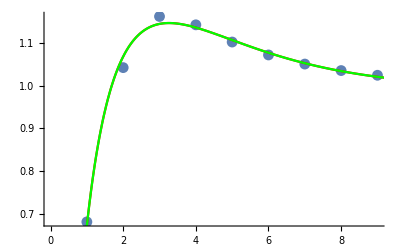

```mathematica
logModel=a;
logModel=a+Log[b*x]*Exp[-c*x];
logFit=FindFit[a/.divCoeffsA,logModel,{{a,1},{b,1,0.1,10},{c,1}},{x}]
glamour=Function[{x},logModel/.logFit];
Show[
ListPlot[a/.divCoeffsA,PlotRange->All],
Plot[logModel/.logFit,{x,0,10},PlotRange->All,PlotStyle->Red],
Plot[glamour[x],{x,0,10},PlotRange->All,PlotStyle->Green]
]
```

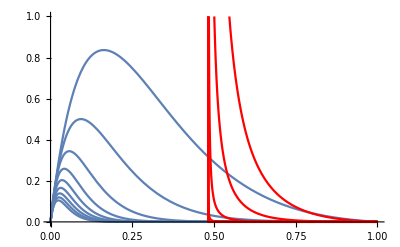

```mathematica
Show[
Table[Plot[funcs[[i]][x],{x,0,1},PlotRange->All],{i,2,bouncesCount}],
Table[Plot[funcs[[i-1]][x]*(Exp[-defB*x]/glamour[i-1]),{x,0,1},PlotStyle->Red,PlotRange->{{0,10},{0,1}}],{i,2,bouncesCount}]
]
```

## Shifting Perspective

What if we tried to use the initial f1 curve’s coefficient over itself multiple times, as we’ll certainly do it in code?
That requires shifting the curves on themselves:

```mathematica
ta=Table[ funcs[[i]][1]/.x-> 0.5,{i,1,bouncesCount}];
ListLinePlot[ta,PlotRange->{{0,10},{0,π/2}}];
```

```mathematica
Manipulate[ListLinePlot[Table[ funcs[[i]][1]/.x-> t ,{i,1,bouncesCount}],PlotRange->{{1,10},{0,π/2}}],{{t,0.5},0,1}]
```

```mathematica
ta3D=Table[Table[ funcs[[i]][1]/.x-> t/100,{i,1,bouncesCount}],{t,0,100}];
ta3D=Table[Table[ (funcs[[i]][1]/.x-> t/100)/(t/100*(1-t/100)),{i,1,bouncesCount}],{t,10,99}];
ListPlot3D[ta3D,PlotRange->All]
```

-Graphics3D-

Intuively, removing the α(1-α) shows us some sort of regular exponential decay whose decay rate is correlated to α as well...
Let’s try and see if that’s also the case with the original curves:

```mathematica
ta3D=Table[ Table[bounces[[i]][[j]][[2]],{j,1,100}],{i,1,bouncesCount}];
ta3D=Table[Table[ (bounces[[i]][[j]][[2]])/Max[0.01,(j-1)/99*(1-(j-1)/99)],{i,1,bouncesCount}],{j,1,100}];
MatrixForm[ta3D];
ListPlot3D[ta3D,PlotRange->All,AxesLabel->{"Bounces","α","Amplitude"}]
```

-Graphics3D-

Let’s try and fit the initial bounce value with an exponential:

{{1/11,10.062},{19/99,8.30058},{29/99,6.59232},{13/33,5.56611},{49/99,4.8249},{59/99,4.31694},{23/33,3.88192},{79/99,3.58703},{89/99,3.47447}}

{a→12.255,b→-26.1448,c→27.5502,d→-10.4155}

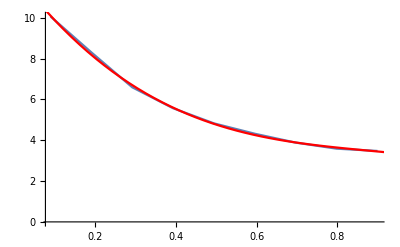

```mathematica
Clear[α,x]
modelA0=9.239635202619764*Exp[-b*(α-1)];
modelA0=a*Exp[-b*α];
modelA0=a+b*α+c*α^2+d*α^3;
samplesCount=Length[ta3D];
coeffsA0=Table[{(i-1)/(samplesCount-1),ta3D[[i]][[1]]},{i,10,90,10}]
fitA0=FindFit[coeffsA0,modelA0,{a,b,c,d},{α}]
fA0=Function[{α},modelA0/.fitA0];
Show[
ListLinePlot[coeffsA0,PlotRange->All],
Plot[fA0[α],{α,0,1},PlotRange->All,PlotStyle->Red]
]
```

Now let’s find a rule to drive the decay factor as a function of α :

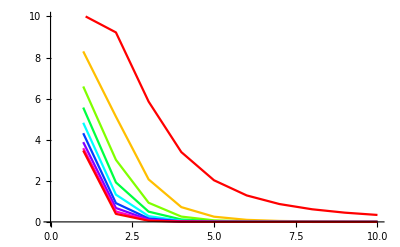

```mathematica
ta3Dortho=Transpose@ta3D;
Show[Table[ListLinePlot[ta3D[[sampleIndex]],PlotRange->{0,10},PlotStyle->Hue[(sampleIndex-10)/80]],{sampleIndex,10,90,10}]]
```

{6.59232,3.02221,0.931351,0.258434,0.0757342,0.0261872,0.0112131,0.00586212,0.00356892,0.00240701}

6.6099

6.6099 ⅇ^(-b (-1+x))

{a→1.,b→0.887286}

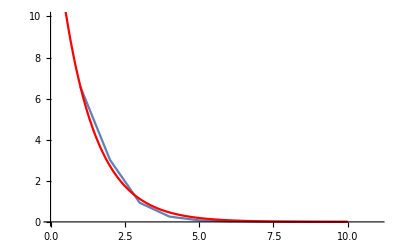

```mathematica
α=0.3;
sampleIndex=Round[α*samplesCount];
ta3D[[sampleIndex]]
A0=fA0[α]
modelDecay=A0*Exp[-b*(x-1)];
modelDecay=fA0[α]*Exp[-b*(x-1)]
fitDecay=FindFit[ta3D[[sampleIndex]],modelDecay,{a,b},{x}]
fDecay=Function[{x},modelDecay/.fitDecay];
Show[
ListLinePlot[ta3D[[sampleIndex]],PlotRange->{{0,11},{0,bouncesCount}}],
Plot[modelDecay/.fitDecay/.x-> bounceIndex,{bounceIndex,0,bouncesCount},PlotRange->Full,PlotStyle->Red]
]
```

Applying to many samples, we get a list of coefficients depending on α

{{x→0.1,a→9.90564,b→0.332558},{x→0.15,a→8.91804,b→0.493305},{x→0.2,a→8.04476,b→0.641783},{x→0.25,a→7.27798,b→0.775267},{x→0.3,a→6.6099,b→0.887286},{x→0.35,a→6.0327,b→1.00709},{x→0.4,a→5.53856,b→1.11093},{x→0.45,a→5.11968,b→1.20334},{x→0.5,a→4.76825,b→1.31264},{x→0.55,a→4.47646,b→1.40085},{x→0.6,a→4.23648,b→1.54751},{x→0.65,a→4.04052,b→1.62502},{x→0.7,a→3.88076,b→1.75134},{x→0.75,a→3.74938,b→1.84375},{x→0.8,a→3.63858,b→1.97268},{x→0.85,a→3.54054,b→2.0899},{x→0.9,a→3.44746,b→2.1728}}

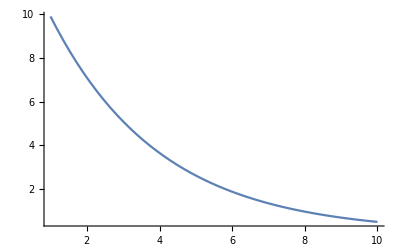

```mathematica
Clear[a,b]
fitter[α_]:=Module[{},
sampleIndex=Round[α*samplesCount];
A0=fA0[α];
modelDecay=A0*Exp[-b*(x-1)];
{x->α,a-> A0, FindFit[ta3D[[sampleIndex]],modelDecay,{b},{x}][[1]]}
]
fitsDecay=Table[fitter[α],{α,0.1,0.9,0.05}]
Plot[a*Exp[-b*(x-1)]/.fitsDecay[[1]],{x,1,bouncesCount},PlotRange->Full]
```

{{0.1,0.332558},{0.15,0.493305},{0.2,0.641783},{0.25,0.775267},{0.3,0.887286},{0.35,1.00709},{0.4,1.11093},{0.45,1.20334},{0.5,1.31264},{0.55,1.40085},{0.6,1.54751},{0.65,1.62502},{0.7,1.75134},{0.75,1.84375},{0.8,1.97268},{0.85,2.0899},{0.9,2.1728}}

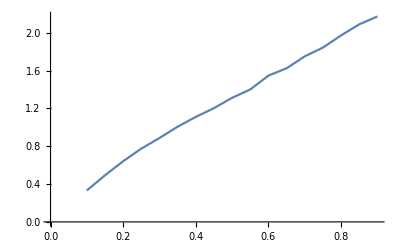

```mathematica
coeffsDecay={x,b}/.fitsDecay
ListLinePlot[coeffsDecay]
```

It looks a lot (!!) like a linear fit! <3

{a→0.186195,b→2.23562}

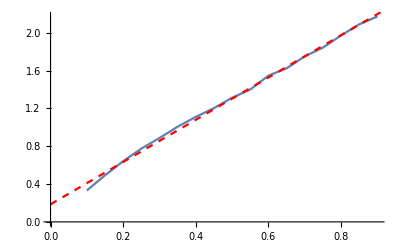

```mathematica
Clear[a,b,α]
modelCoeffsDecay=a+b*α;
fitCoeffsDecay=FindFit[coeffsDecay,modelCoeffsDecay,{a,b},{α}]
Show[
ListLinePlot[coeffsDecay],
Plot[modelCoeffsDecay/.fitCoeffsDecay,{α,0,1},PlotStyle->{Red,Dashed}]
]
```

## Putting it all together!

Okay so now it looks like we have it all: each curve for each bounce i is of the form f_i(α)=A_i*α*(1-α)*e^-B_iα as stated at the beginning of the document.
We later tried to shift our perspective to see, for a given α=AO/π, the shape of the curve we get for each new bounce and it looks like a simple exponential g(α,i)=A(α)ⅇ^(-B(α)i) with an initial amplitude A(α) and a decay factor B(α).
A very good fit for A(α)=12.255-26.1448α+27.5502 α^2-10.4155 α^3 that allows us to find a very simple linear fit for B(α)=0.186195+2.23562α

```mathematica
Clear[A,B]
A[α_]:=12.255-26.144751371564944α+27.5502 α^2-10.4155 α^3
B[α_]:=0.18619452933736622+2.235617876545042α
```

```mathematica
Manipulate[Plot[A[α]*Exp[-B[α]*x],{x,1,10},PlotRange->{0,10}],{{α,0},0,1}]
```

Let’s verify the curves fit our experimental data:

```mathematica
Manipulate[
Show[
ListLinePlot[ta3D[[Round[1+100*α]]],PlotRange->{0,10}],
Plot[A[α]*Exp[-B[α]*(x-1)],{x,1,10},PlotRange->{0,10},PlotStyle->Red]
],{{α,0.2},0,1}]
```

Now, we re-plot the entire data and final curves, with the attenuation curve:

```mathematica
(*finalTable3D=Table[Table[ (bounces[[i]][[j]][[2]])/Max[0.01,(j-1)/99*(1-(j-1)/99)],{i,1,bouncesCount}],{j,1,100}];*)
finalTable3D=Table[Table[ bounces[[i]][[j]][[2]],{i,1,bouncesCount}],{j,1,100}];
reconstructedTable3D=Table[Table[ α*(1-α)*A[α]*Exp[-B[α]*(i-1)],{i,1,bouncesCount}],{α,0,1,0.01}];
Show[ListPlot3D[finalTable3D,PlotRange->{0,π/2},AxesLabel->{"Bounces","α","Amplitude"}],
ListPlot3D[reconstructedTable3D,PlotRange->{0,π/2},AxesLabel->{"Bounces","α","Amplitude"},PlotStyle->Red]]
```

-Graphics3D-

So basically, in the shader, all we need to do is computing A_0=α(1-α)A(α) and K=ρ.ⅇ^(-B(α)) then the final expression for outgoing luminance is given by:

	L(x,ω_o)=ρ/π.AO +A_0/π ∑_(i=1)^∞ K^i

```mathematica
Manipulate[
A0=A[α];
K0=Exp[-B[α]];
Show[
ListPlot[Table[α*(1-α)*A0*Product[K0,{i,maxI}],{maxI,1,bouncesCount}],PlotRange->{0,π/4}],
Plot[α*(1-α)*A0*Exp[-B[α]*x],{x,1,10},PlotRange->All,PlotStyle->Red]
],{{α,0.1},0,1}]
```

Final verification with the 50% albedo table:

```mathematica
ρ=0.5;
finalTable3D=Table[Table[ bounces05[[i]][[j]][[2]],{i,1,bouncesCount}],{j,1,100}];
reconstructedTable3D=Table[Table[ α*(1-α)*A[α]*ρ^i*Exp[-B[α]*(i-1)],{i,1,bouncesCount}],{α,0,1,0.01}];
Show[ListPlot3D[finalTable3D,PlotRange->{0,π/4},AxesLabel->{"Bounces","α","Amplitude"}],
ListPlot3D[reconstructedTable3D,PlotRange->{0,π/2},AxesLabel->{"Bounces","α","Amplitude"},PlotStyle->Red]]
```

-Graphics3D-

Part::partw: Part 10 of {{a → 0.680573}, {a → 1.04274}, {a → 1.16286}, {a → 1.14321}, {a → 1.10282}, {a → 1.0725}, {a → 1.05111}, {a → 1.03584}, {a → 1.0248}} does not exist.

ReplaceAll::reps: {{{a → 0.680573}, {a → 1.04274}, {a → 1.16286}, {a → 1.14321}, {a → 1.10282}, {a → 1.0725}, {a → 1.05111}, {a → 1.03584}, {a → 1.0248}} ⟦ 10 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

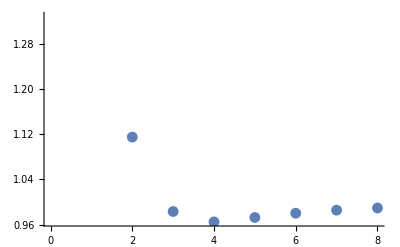

```mathematica
ListPlot[Table[(a/.divCoeffsA[[i]])/(a/.divCoeffsA[[i-1]]),{i,2,bouncesCount}]]
```

{a→2.63648,b→3.38627}

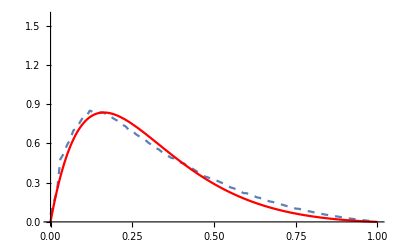

```mathematica
f1=Function[{x},model/.fits[[1]]];
Plot[f1[x],{x,0,1}];
model2=f1[x]*b/a*Exp[-b*x];
fit2=FindFit[bounces[[2]],model2,{a,b},{x}]
f2=Function[{x},model2/.fit2];
Show[
ListLinePlot[bounces[[2]],PlotRange->{{0,1},{0,π/2}},PlotStyle->Dashed],
Plot[f2[x],{x,0,1},PlotRange->Full,PlotStyle->Red]
]
```

{a→4.42749,b→4.69113}

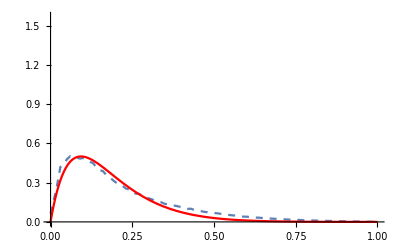

```mathematica
model3=f2[x]*b/a*Exp[-b*x];
fit3=FindFit[bounces[[3]],model3,{a,b},{x}]
f3=Function[{x},model3/.fit3];
Show[
ListLinePlot[bounces[[3]],PlotRange->{{0,1},{0,π/2}},PlotStyle->Dashed],
Plot[f3[x],{x,0,1},PlotRange->Full,PlotStyle->Red]
]
```

{a→6.02535,b→6.75756}

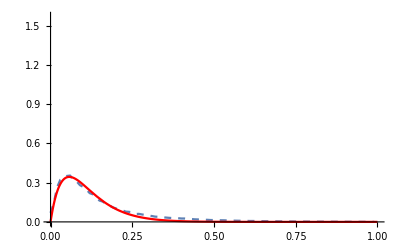

```mathematica
model4=f3[x]*b/a*Exp[-b*x];
fit4=FindFit[bounces[[4]],model4,{a,b},{x}]
f4=Function[{x},model4/.fit4];
Show[
ListLinePlot[bounces[[4]],PlotRange->{{0,1},{0,π/2}},PlotStyle->Dashed],
Plot[f4[x],{x,0,1},PlotRange->Full,PlotStyle->Red]
]
```

{a→6.17637,b→6.32656}

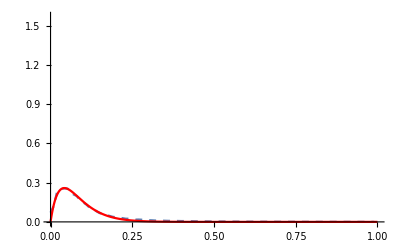

```mathematica
model5=f4[x]*b/a*Exp[-b*x];
fit5=FindFit[bounces[[5]],model5,{a,b},{x}]
f5=Function[{x},model5/.fit5];
Show[
ListLinePlot[bounces[[5]],PlotRange->{{0,1},{0,π/2}},PlotStyle->Dashed],
Plot[f5[x],{x,0,1},PlotRange->Full,PlotStyle->Red]
]
```

{a→0.145266,b→1.55043}

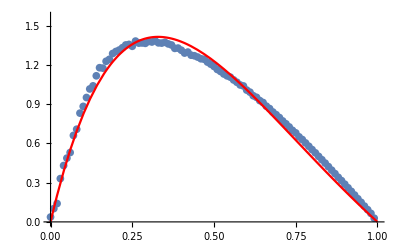

```mathematica
modelFit1=FindFit[bounces[[1]], model,{a,b},{x}]
bounce1=Function[{x},Evaluate[model/.modelFit1]];
Show[
ListPlot[bounces[[1]],PlotRange->{{0,1},{0,π/2}}],
Plot[bounce1[x],{x,0,1},PlotStyle->Red]
]
```

{a→0.360125,b→4.9367}

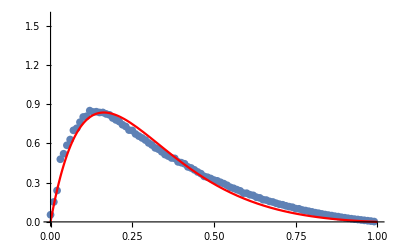

```mathematica
modelFit2=FindFit[bounces[[2]], model,{a,b},{x}]
bounce2=Function[{x},Evaluate[model/.modelFit2]];
Show[
ListPlot[bounces[[2]],PlotRange->{{0,1},{0,π/2}}],
Plot[bounce2[x],{x,0,1},PlotStyle->Red]
]
```

{a→0.662865,b→9.62783}

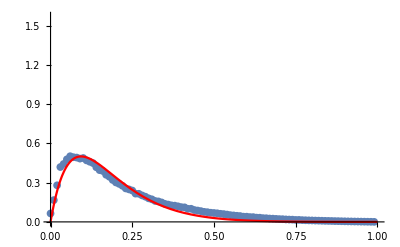

```mathematica
modelFit3=FindFit[bounces[[3]], model,{a,b},{x}]
bounce3=Function[{x},Evaluate[model/.modelFit3]];
Show[
ListPlot[bounces[[3]],PlotRange->{{0,1},{0,π/2}}],
Plot[bounce3[x],{x,0,1},PlotStyle->Red]
]
```

{a→1.00588,b→16.3854}

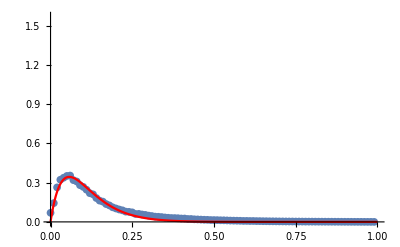

```mathematica
modelFit4=FindFit[bounces[[4]], model,{a,b},{x}]
bounce4=Function[{x},Evaluate[model/.modelFit4]];
Show[
ListPlot[bounces[[4]],PlotRange->{{0,1},{0,π/2}}],
Plot[bounce4[x],{x,0,1},PlotStyle->Red]
]
```

{0.145266,0.360125,0.662865,1.00588}

{1.55043,4.9367,9.62783,16.3854}

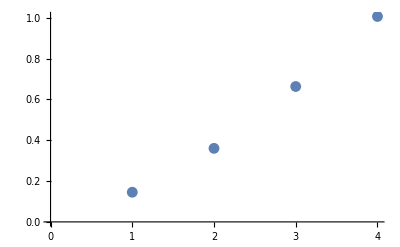

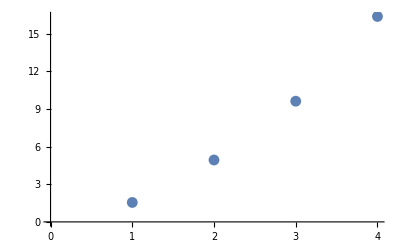

```mathematica
coeffsA={a/.modelFit1,a/.modelFit2,a/.modelFit3,a/.modelFit4}
coeffsB={b/.modelFit1,b/.modelFit2,b/.modelFit3,b/.modelFit4}
ListPlot[coeffsA]
ListPlot[coeffsB]
```